```mathematica
μ[λ_,ρ_]:=λ/(2ρ)
μ[0.25,{0.55}]
Clear["Global`*"] (*Clear all global Variables*)
```

{0.227273}

## Define Theoretical Equations

```mathematica
Clear[λ,μ]
P0[ρ_]:=(1-ρ)/(1-ρ^11) (*Stationary Distribution*)
P[ρ_,n_]:=P0[ρ]*ρ^n (*Prob of being in state n*)
PBlock[ρ_]:=P[ρ,10](*Blocking Probability*)
L[ρ_]:=∑_(n=0)^10 n*P[ρ,n](*AVG num of Customers*)
B[ρ_]:= 1-P0[ρ](*AVG num of Cust being Served*)
Lq[ρ_]:=(L[ρ]-B[ρ] )(*Avergae Que Length*)
S[ρ_,λ_]:=L[ρ]/λ(*AVG sojourn time*)
S2[ρ_,μ_]:=1/(2μ)*(1-11 ρ^10+10 ρ^11)/((1-ρ)(1-ρ^11))(*AVG sojourn time in terms of μ*)
```

## Define Plots

```mathematica
TheorPlot[title_,f_,domain_,range_,xLabel_,yLabel_] := Plot[f,domain,
PlotRange->range,
AxesLabel->{xLabel,yLabel},
PlotLabel->title,
PlotStyle->Black,PlotLegends->{"Theoretical"}
]
S1Plot[x_,y_]:= ListPlot[
Transpose[{x,y}],
PlotStyle->Red,PlotLegends->{"Strategy 1"}
]
S2Plot[x_,y_]:= ListPlot[
Transpose[{x,y}],
PlotStyle->Blue,PlotLegends->{"Strategy 2"}
]
```

## Blocking Probability

### λ Plot (Set μ = 0.5) (λ → {0,1} )

```mathematica
x = {0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0};
S1y = ConstantArray[0,11];
S2y = ConstantArray[0,11];
```

#### Strategy 1 Data

```mathematica
S1y[[1]]=Mean[{0}]; (*λ=0*)
S1y[[2]]=Mean[{0}];(*λ=0.1*)
S1y[[3]]=Mean[{0}];(*λ=0.2*)
S1y[[4]]=Mean[{0}];(*λ=0.3*)
S1y[[5]]=Mean[{0.00020000,0.00080000,0.00010000,0.00070000,0.00040000,0.00010000,0.00010000,0.00030000,0.00030000,0.00030000}];(*λ=0.4*)
S1y[[6]]=Mean[{0.00040000,0.00080000,0.00060000,0.00130000,0.00050000,0.00050000,0.00040000,0.00110000,0.00060000,0.00020000}]; (*λ=0.5*)
S1y[[7]]=Mean[{0.00290000,0.00280000,0.00270000,0.00070000,0.00150000,0.00170000,0.00320000,0.00210000,0.00210000,0.00330000}]; (*λ=0.6*)
S1y[[8]]=Mean[{0.00570000,0.01010000,0.00620000,0.00840000,0.01080000,0.00860000,0.00470000,0.00860000,0.01050000,0.00610000}]; (*λ=0.7*)
S1y[[9]]=Mean[{0.02390000,0.02260000,0.02280000,0.02410000,0.02550000,0.02280000,0.02290000,0.02660000,0.02300000,0.02060000}]; (*λ=0.8*)
S1y[[10]]=Mean[{0.04710000,0.05100000,0.06320000,0.04000000,0.04990000,0.04160000,0.05090000,0.05300000,0.05440000,0.05520000}]; (*λ=0.9*)
S1y[[11]]=Mean[{0.09290000,0.07630000,0.08790000,0.08740000,0.07350000,0.09100000,0.09790000,0.09500000,0.09050000,0.08940000}];(*λ=1.0*)
```

#### Strategy 2 Data

```mathematica
S2y[[2]]=Mean[{0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000}]; (*λ=0.10*)
S2y[[3]]=Mean[{0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000}]; (*λ=0.20*)
S2y[[4]]=Mean[{0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000}]; (*λ=0.30*)
S2y[[5]]=Mean[{0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000}]; (*λ=0.40*)
S2y[[6]]=Mean[{0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000}]; (*λ=0.50*)
S2y[[7]]=Mean[{0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000}]; (*λ=0.60*)
S2y[[8]]=Mean[{0.00000000,0.00000000,0.00000000,0.00040000,0.00200000,0.00000000,0.00060000,0.00090000,0.00060000,0.00010000}]; (*λ=0.70*)
S2y[[9]]=Mean[{0.00230000,0.00290000,0.00070000,0.00620000,0.00130000,0.00500000,0.00240000,0.00180000,0.00350000,0.00370000}]; (*λ=0.80*)
S2y[[10]]=Mean[{0.01430000,0.01600000,0.01000000,0.01140000,0.01450000,0.01620000,0.01230000,0.01530000,0.01650000,0.01860000}]; (*λ=0.90*)
S2y[[11]]=Mean[{0.04160000,0.04540000,0.03900000,0.04110000,0.05670000,0.05390000,0.05540000,0.05790000,0.04950000,0.03740000}]; (*λ=1.00*)
```

#### Plot

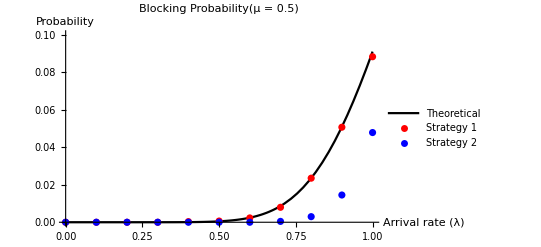

```mathematica
p1 =TheorPlot["Blocking Probability(μ  = 0.5)",PBlock[λ/(2(0.5))],{λ,0,1},{0,0.1},"Arrival rate (λ)","Probability"];
Show[p1, S1Plot[x,S1y],S2Plot[x,S2y]]
```

### μ Plot (Set λ = 10) (μ → {0.5,6} )

```mathematica
x = {0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,6};
S1y = ConstantArray[0,11];
S2y = ConstantArray[0,11];
```

#### Strategy 1 Data

```mathematica
S1y[[1]]=Mean[{0.90330000,0.90200000,0.89730000,0.89910000,0.89550000,0.89820000,0.89990000,0.89640000,0.89620000,0.89750000}]; (*μ=0.50*)
S1y[[2]]=Mean[{0.80580000,0.80080000,0.80190000,0.80010000,0.80070000,0.80870000,0.79440000,0.79050000,0.78830000,0.79790000}]; (*μ=1.00*)
S1y[[3]]=Mean[{0.69400000,0.69550000,0.69580000,0.69360000,0.69200000,0.70470000,0.70510000,0.69670000,0.70800000,0.70220000}]; (*μ=1.50*)
S1y[[4]]=Mean[{0.60680000,0.59170000,0.61240000,0.59670000,0.60060000,0.59700000,0.58380000,0.60910000,0.59160000,0.60020000}]; (*μ=2.00*)
S1y[[5]]=Mean[{0.50860000,0.48790000,0.50610000,0.49550000,0.50470000,0.50210000,0.49460000,0.49760000,0.50210000,0.50400000}]; (*μ=2.50*)
S1y[[6]]=Mean[{0.40310000,0.40290000,0.40000000,0.41110000,0.41850000,0.39860000,0.38800000,0.41550000,0.39420000,0.40980000}]; (*μ=3.00*)
S1y[[7]]=Mean[{0.30740000,0.28270000,0.29560000,0.30150000,0.30840000,0.31150000,0.29290000,0.32740000,0.29490000,0.32890000}]; (*μ=3.50*)
S1y[[8]]=Mean[{0.21330000,0.20230000,0.21920000,0.21330000,0.21640000,0.23030000,0.22590000,0.21420000,0.20640000,0.22570000}]; (*μ=4.00*)
S1y[[9]]=Mean[{0.13870000,0.12980000,0.14120000,0.13180000,0.12760000,0.13220000,0.13780000,0.14860000,0.16200000,0.14720000}]; (*μ=4.50*)
S1y[[10]]=Mean[{0.08190000,0.09200000,0.09950000,0.10660000,0.09290000,0.10080000,0.07570000,0.09560000,0.07550000,0.07880000}]; (*μ=5.00*)
S1y[[11]]=Mean[{0.03270000,0.03810000,0.02960000,0.03180000,0.02840000,0.03310000,0.03110000,0.02430000,0.03530000,0.02970000}]; (*μ=6.00*)
```

#### Strategy 2 Data

```mathematica
S2y[[1]]=Mean[{0.90360000,0.89720000,0.89970000,0.89720000,0.89760000,0.89520000,0.89650000,0.89840000,0.89910000,0.89610000}]; (*μ=0.50*)
S2y[[2]]=Mean[{0.81070000,0.79540000,0.79850000,0.79900000,0.79970000,0.80590000,0.80410000,0.80230000,0.80560000,0.79450000}]; (*μ=1.00*)
S2y[[3]]=Mean[{0.70770000,0.70340000,0.70220000,0.69820000,0.69520000,0.70320000,0.69850000,0.70220000,0.69950000,0.70170000}]; (*μ=1.50*)
S2y[[4]]=Mean[{0.59820000,0.58790000,0.60360000,0.58450000,0.59940000,0.58210000,0.59390000,0.58890000,0.60540000,0.60190000}]; (*μ=2.00*)
S2y[[5]]=Mean[{0.49030000,0.48710000,0.49970000,0.49900000,0.49380000,0.50130000,0.50110000,0.49250000,0.49840000,0.49410000}]; (*μ=2.50*)
S2y[[6]]=Mean[{0.39500000,0.41120000,0.41090000,0.39800000,0.39990000,0.39410000,0.38380000,0.40080000,0.39800000,0.40120000}]; (*μ=3.00*)
S2y[[7]]=Mean[{0.30210000,0.29730000,0.29220000,0.29440000,0.29060000,0.30140000,0.29240000,0.30420000,0.30960000,0.27610000}]; (*μ=3.50*)
S2y[[8]]=Mean[{0.22260000,0.22290000,0.19090000,0.19620000,0.18850000,0.20140000,0.19270000,0.22510000,0.20750000,0.19920000}]; (*μ=4.00*)
S2y[[9]]=Mean[{0.10600000,0.11380000,0.11970000,0.13180000,0.11210000,0.11180000,0.13920000,0.10210000,0.10610000,0.10630000}]; (*μ=4.50*)
S2y[[10]]=Mean[{0.05320000,0.04360000,0.05130000,0.07060000,0.06900000,0.05620000,0.04920000,0.05300000,0.04680000,0.0381000}]; (*μ=5.00*)
S2y[[11]]=Mean[{0.00450000,0.00620000,0.00400000,0.00510000,0.00830000,0.01020000,0.00430000,0.00540000,0.00780000,0.00380000}]; (*μ=6.00*)
```

#### Plot

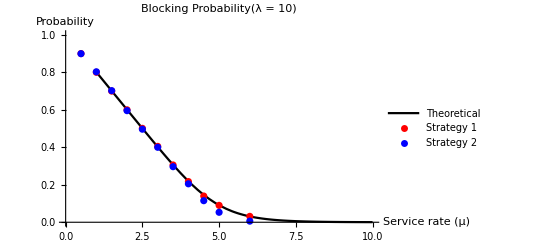

```mathematica
p1 =TheorPlot["Blocking Probability(λ  = 10)",PBlock[10/(2μ)],{μ,1,10},{0,1},"Service rate (μ)","Probability"];
Show[p1, S1Plot[x,S1y],S2Plot[x,S2y]]
```

### ρ Plot (Choose and λ, μ such that ρ -> {0, 1})

```mathematica
x1= {0.55,0.6,0.65}; (*ρ values*)
x2= {0.7,0.75,0.8}; (*ρ values*)
x3= {0.85,0.9,0.95}; (*ρ values*)

S1y1 = ConstantArray[0,3];
S1y2 = ConstantArray[0,3];
S1y3 = ConstantArray[0,3];

S2y1 = ConstantArray[0,3];
S2y2 = ConstantArray[0,3];
S2y3 = ConstantArray[0,3];
```

#### Strategy 1 Data

```mathematica
(*λ = 0.25*)
S1y1[[1]]=Mean[{0.00120000,0.00080000,0.00140000,0.00130000,0.00140000,0.00110000,0.00040000,0.00070000,0.00170000,0.00040000}]; (*μ=0.23*)
S1y1[[2]]=Mean[{0.00220000,0.00410000,0.00230000,0.00180000,0.00100000,0.00130000,0.00360000,0.00230000,0.00110000,0.00190000}]; (*μ=0.21*)
S1y1[[3]]=Mean[{0.00530000,0.00650000,0.00680000,0.00360000,0.00540000,0.00490000,0.00550000,0.00520000,0.00490000,0.00590000}]; (*μ=0.19*)
(*λ = 5*)
S1y2[[1]]=Mean[{0.00960000,0.00940000,0.01110000,0.00530000,0.00910000,0.00930000,0.00820000,0.01010000,0.00560000,0.00800000}]; (*μ=3.57*)
S1y2[[2]]=Mean[{0.02030000,0.01190000,0.01290000,0.01110000,0.01540000,0.01130000,0.01350000,0.01790000,0.01360000,0.01610000}]; (*μ=3.33*)
S1y2[[3]]=Mean[{0.02550000,0.02840000,0.02380000,0.01850000,0.02340000,0.02330000,0.02530000,0.02360000,0.02460000,0.02450000}]; (*μ=3.12*)
(*λ = 0.25*)
S1y3[[1]]=Mean[{0.03780000,0.02940000,0.03280000,0.03650000,0.03210000,0.03430000,0.03580000,0.03160000,0.03200000,0.03290000}]; (*μ=5.88*)
S1y3[[2]]=Mean[{0.05400000,0.04470000,0.04160000,0.05440000,0.04710000,0.04790000,0.04520000,0.05570000,0.05110000,0.04850000}]; (*μ=5.56*)
S1y3[[3]]=Mean[{0.07280000,0.06320000,0.07420000,0.06770000,0.06580000,0.07610000,0.06780000,0.06570000,0.06360000,0.06390000}]; (*μ=5.26*)
```

#### Strategy 2 Data

```mathematica
(*λ = 0.25*)
S2y1[[1]]=Mean[{0.00000000,0.00020000,0.00000000,0.00000000,0.00000000,0.00000000,0.00010000,0.00000000,0.00000000,0.00000000}]; (*μ=0.23*)
S2y1[[2]]=Mean[{0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000}]; (*μ=0.21*)
S2y1[[3]]=Mean[{0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00050000,0.00000000}]; (*μ=0.19*)
(*λ = 5*)
S2y2[[1]]=Mean[{0.00000000,0.00040000,0.00020000,0.00000000,0.00000000,0.00030000,0.00000000,0.00030000,0.00110000,0.00030000}]; (*μ=3.57*)
S2y2[[2]]=Mean[{0.00000000,0.00120000,0.00040000,0.00200000,0.00080000,0.00050000,0.00150000,0.00110000,0.00020000,0.00250000}]; (*μ=3.33*)
S2y2[[3]]=Mean[{0.00500000,0.00150000,0.00160000,0.00220000,0.00230000,0.00480000,0.00190000,0.00440000,0.00760000,0.00040000}]; (*μ=3.12*)
(*λ = 0.25*)
S2y3[[1]]=Mean[{0.00530000,0.00100000,0.00510000,0.00430000,0.00510000,0.00480000,0.00960000,0.00530000,0.01110000,0.00720000}]; (*μ=5.88*)
S2y3[[2]]=Mean[{0.02040000,0.01860000,0.01350000,0.01920000,0.02020000,0.01450000,0.01410000,0.00950000,0.01570000,0.01420000}]; (*μ=5.56*)
S2y3[[3]]=Mean[{0.03010000,0.03410000,0.03260000,0.02090000,0.04240000,0.02990000,0.04180000,0.03430000,0.02490000,0.02160000}]; (*μ=5.26*)
```

#### Plot

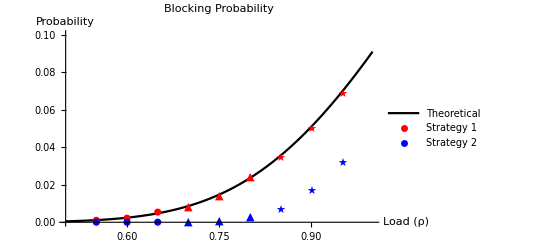

```mathematica
p1 =TheorPlot["Blocking Probability",PBlock[ρ],{ρ,0.5,1},{0,0.1},"Load (ρ)","Probability"];
Show[
p1,
ListPlot[Transpose[{x1,S1y1}],PlotStyle->Red,PlotLegends->{"Strategy 1"}],
ListPlot[Transpose[{x2,S1y2}],PlotStyle->Red,PlotMarkers->"▲"],
ListPlot[Transpose[{x3,S1y3}],PlotStyle->Red,PlotMarkers->"★"],

ListPlot[Transpose[{x1,S2y1}],PlotStyle->Blue,PlotLegends->{"Strategy 2"}],
ListPlot[Transpose[{x2,S2y2}],PlotStyle->Blue,PlotMarkers->"▲"],
ListPlot[Transpose[{x3,S2y3}],PlotStyle->Blue,PlotMarkers->"★"]
]
```

## Avg Queue Length

### λ Plot (Set μ = 0.5) (λ → {0,1} )

```mathematica
x = {0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0};
S1y = ConstantArray[0,11];
S2y = ConstantArray[0,11];
```

#### Strategy 1 Data

```mathematica
S1y[[1]]=Mean[{0}]; (*λ=0*)
S1y[[2]]=Mean[{0.27812155,0.27917982,0.28234235,0.28090437,0.27502422,0.28645980,0.27658120,0.28248534,0.27864799,0.28441944}];(*λ=0.1*)
S1y[[3]]=Mean[{0.37377244,0.37434106,0.36735607,0.37049987,0.36969532,0.37577329,0.37040802,0.36448019,0.37435922,0.35998759}];(*λ=0.2*)
S1y[[4]]=Mean[{0.51743916,0.50252138,0.50906737,0.50049042,0.49016755,0.52232179,0.49602856,0.50990367,0.50988298,0.52593151}];(*λ=0.3*)
S1y[[5]]=Mean[{0.73476267,0.69990102,0.75399391,0.73976738,0.72359324,0.72103923,0.70397074,0.71805659,0.71411848,0.76674931}];(*λ=0.4*)
S1y[[6]]=Mean[{1.01879753,1.01701309,1.04208395,1.01036931,0.98754096,1.03305731,1.14035776,1.02687181,0.97531187,1.02095626}]; (*λ=0.5*)
S1y[[7]]=Mean[{1.44743815,1.44860866,1.44407298,1.36778045,1.48151663,1.34187540,1.39496826,1.38280814,1.27519000,1.52493177}]; (*λ=0.6*)
S1y[[8]]=Mean[{2.17281628,2.22497492,1.87851589,2.27955924,2.32348960,2.19455385,2.24494741,2.17282426,2.33799616,2.08365685}]; (*λ=0.7*)
S1y[[9]]=Mean[{3.01138635,3.06190401,2.87510925,2.99500267,2.86024615,3.19179502,3.24316800,2.91313481,3.04060059,2.93322356}]; (*λ=0.8*)
S1y[[10]]=Mean[{4.28144685,3.95490748,4.08620737,4.34640016,3.72486657,4.13716406,4.00421790,3.80950294,4.19516992,3.79053123}]; (*λ=0.9*)
S1y[[11]]=Mean[{4.97668359,5.16543192,4.98147021,4.59681840,5.05998187,4.77437066,5.36041912,4.83778264,4.84485931,5.24269465}];(*λ=1.0*)
```

#### Strategy 2 Data

```mathematica
S1y[[1]]=Mean[{0}]; (*λ=0*)
S2y[[2]]=Mean[{0.06536979,0.06260068,0.06314546,0.06170620,0.06537324,0.06155913,0.06481835,0.06260530,0.06361561,0.06407284}]; (*λ=0.10*)
S2y[[3]]=Mean[{0.14010236,0.14830631,0.15175047,0.14828312,0.14985400,0.15086532,0.13928507,0.14890547,0.15173436,0.14527867}]; (*λ=0.20*)
S2y[[4]]=Mean[{0.26691398,0.26607286,0.24384213,0.25653151,0.26549190,0.26256204,0.25655009,0.26041379,0.24434903,0.25690492}]; (*λ=0.30*)
S2y[[5]]=Mean[{0.39844645,0.39823027,0.36514624,0.42321004,0.39746349,0.38884520,0.40294212,0.40224320,0.40056832,0.39835945}]; (*λ=0.40*)
S2y[[6]]=Mean[{0.60638956,0.57368729,0.57228816,0.61268530,0.59636510,0.60368014,0.61229289,0.53986456,0.57039908,0.57009240}]; (*λ=0.50*)
S2y[[7]]=Mean[{0.92129219,0.84704801,0.92742352,0.81322572,0.91591046,0.80728829,0.88015422,0.83200355,0.84766603,0.78955210}]; (*λ=0.60*)
S2y[[8]]=Mean[{1.34565792,1.27800541,1.34146606,1.34536363,1.14118692,1.25015832,1.36150801,1.32801485,1.25419905,1.24166143}]; (*λ=0.70*)
S2y[[9]]=Mean[{1.91260828,1.92923642,2.07157608,2.21098656,1.94939997,2.02207486,1.96543719,1.94357444,2.12280338,2.28713070}]; (*λ=0.80*)
S2y[[10]]=Mean[{3.32437087,3.25329095,3.26662087,3.30284874,3.48112319,3.04808354,3.54627297,3.06672230,3.32880023,3.14734413}]; (*λ=0.90*)
S2y[[11]]=Mean[{4.80960050,4.91315249,4.59867643,5.01817104,4.80942355,5.02451455,4.84988595,5.19482993,4.85458417,5.34021811}]; (*λ=1.00*)
```

#### Plot

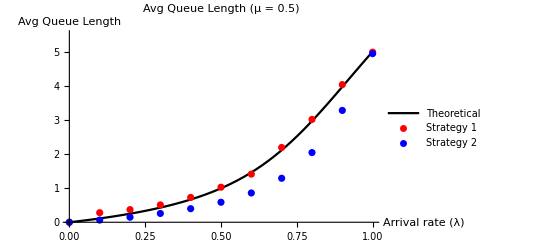

```mathematica
p1 =TheorPlot["Avg Queue Length (μ = 0.5)",L[ρ],{ρ,0,1},{0,5.5},"Arrival rate (λ)","Avg Queue Length"];
Show[p1,S1Plot[x,S1y],S2Plot[x,S2y]]
```

### μ Plot (Set λ = 2) (μ → {1,10} )

```mathematica
x = {1,1.1,1.25,1.4,1.6,2,2.5,3.3,5,8,10};
S1y = ConstantArray[0,11];
S2y = ConstantArray[0,11];
```

#### Strategy 1 Data

```mathematica
S1y[[1]]=Mean[{5.15654684,4.64676863,5.11686747,4.89935683,4.86206061,5.04029537,5.13621760,4.80923353,4.92232986,4.70682343}]; (*μ=1*)
S1y[[2]]=Mean[{4.26765761,4.25699744,4.28892516,4.20443371,3.98112522,3.87089126,3.73844931,3.93255617,3.66781996,3.97195544}];(*μ=1.1*)
S1y[[3]]=Mean[{2.68651599,2.91022056,3.10376675,2.87670642,3.07882353,2.74220542,2.90016994,3.10172297,3.01156660,2.88654398}];(*μ=1.25*)
S1y[[4]]=Mean[{2.21765558,2.35530239,2.28311613,2.08258323,2.42580750,2.31424430,2.17626586,2.32942807,2.16329366,2.09253964}];(*μ=1.4*)
S1y[[5]]=Mean[{1.65615181,1.67112618,1.73244216,1.62104878,1.61497955,1.64538947,1.65410880,1.43843227,1.70073203,1.58076391}];(*μ=1.6*)
S1y[[6]]=Mean[{1.02609193,1.05548183,0.99667838,0.95671957,0.94410881,0.92881340,1.01741182,0.95252708,1.03245211,1.06848971}]; (*μ=2*)
S1y[[7]]=Mean[{0.69164342,0.74272352,0.74923060,0.75718299,0.74740726,0.73255343,0.72972596,0.72208835,0.67032940,0.73173235}]; (*μ=2.5*)
S1y[[8]]=Mean[{0.53903193,0.48850577,0.49377528,0.51816052,0.51763212,0.50821747,0.52422711,0.53620359,0.52353680,0.52625844}]; (*μ=3.3*)
S1y[[9]]=Mean[{0.38411495,0.37586180,0.36841073,0.37813917,0.37132228,0.36124597,0.35787286,0.36319304,0.35725613,0.37132985}]; (*μ=5*)
S1y[[10]]=Mean[{0.28974328,0.30233927,0.30195036,0.29824036,0.29860176,0.29564719,0.28727321,0.30087945,0.29487241,0.30378689}]; (*μ=8*)
S1y[[11]]=Mean[{0.28011530,0.27264588,0.28818681,0.28308032,0.28637158,0.28604515,0.28447798,0.28452140,0.28423670,0.28436819}];(*μ=10*)
```

#### Strategy 2 Data

```mathematica
S2y[[1]]=Mean[{5.19786646,5.15060965,4.84286255,5.26104094,4.93490084,4.74567092,4.60953317,5.12487843,4.92663107,5.12767578}]; (*μ=1*)
S2y[[2]]=Mean[{3.74008988,3.25620033,3.40267702,3.19597965,3.56605478,3.69709312,3.52341817,3.73326767,3.33728377,3.37297789}];(*μ=1.1*)
S2y[[3]]=Mean[{2.03498860,2.00922391,1.85618142,2.07635056,1.94702545,2.11776767,2.05453031,2.07470347,1.90765952,1.89787363}];(*μ=1.25*)
S2y[[4]]=Mean[{1.33001304,1.43062022,1.30211742,1.23641726,1.34073607,1.42613701,1.45356637,1.37322921,1.33993586,1.43285730}];(*μ=1.4*)
S2y[[5]]=Mean[{0.91043087,0.95727056,0.90138416,0.95294305,0.95750773,1.02062940,0.92651476,0.90171067,0.93027219,1.00030335}];(*μ=1.6*)
S2y[[6]]=Mean[{0.59274623,0.60896270,0.59781282,0.60795296,0.57679503,0.58003040,0.58919818,0.59346380,0.58745194,0.58115816}]; (*μ=2*)
S2y[[7]]=Mean[{0.39121316,0.38838408,0.39391456,0.42366643,0.38417500,0.38873560,0.39577165,0.40303291,0.40476277,0.38349866}]; (*μ=2.5*)
S2y[[8]]=Mean[{0.25450092,0.25981602,0.27596353,0.27542135,0.26163984,0.26516716,0.25666549,0.26408336,0.25191659,0.26604067}]; (*μ=3.3*)
S2y[[9]]=Mean[{0.14650723,0.15476159,0.15644808,0.14882674,0.15231502,0.14839239,0.15322316,0.15680978,0.15472419,0.15384838}]; (*μ=5*)
S2y[[10]]=Mean[{0.08213157,0.09009947,0.08269839,0.08553719,0.08192000,0.08664321,0.08374863,0.09149525,0.07927509,0.08188666}]; (*μ=8*)
S2y[[11]]=Mean[{0.06229487,0.06439458,0.06173470,0.06816146,0.06062673,0.06681181,0.06528659,0.06051067,0.06330695,0.06053193}];(*μ=10*)
```

#### Plot

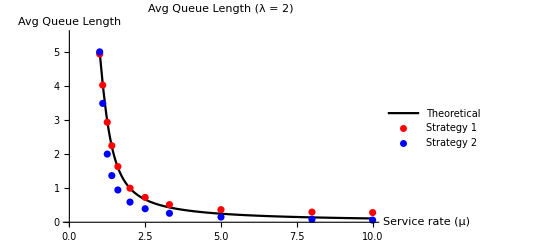

```mathematica
p1 =TheorPlot["Avg Queue Length (λ = 2)",L[2/(2μ)],{μ,1,10},{0,5.5},"Service rate (μ)","Avg Queue Length"];
Show[p1,S1Plot[x,S1y],S2Plot[x,S2y]]
```

### ρ Plot (Choose and λ, μ such that ρ -> {0, 1})

```mathematica
x1= {0.55,0.6,0.65}; (*ρ values*)
x2= {0.7,0.75,0.8}; (*ρ values*)
x3= {0.85,0.9,0.95}; (*ρ values*)

S1y1 = ConstantArray[0,3];
S1y2 = ConstantArray[0,3];
S1y3 = ConstantArray[0,3];

S2y1 = ConstantArray[0,3];
S2y2 = ConstantArray[0,3];
S2y3 = ConstantArray[0,3];
```

#### Strategy 1 Data

```mathematica
(*λ = 0.25*)
S1y1[[1]]=Mean[{1.15531214,1.21869925,1.28900006,1.33386191,1.13682270,1.15290700,1.22556747,1.23430018,1.21660803,1.18684098}]; (*μ=0.23*)
S1y1[[2]]=Mean[{1.51185520,1.39029011,1.35696517,1.38450859,1.59600895,1.49702227,1.44498632,1.55945485,1.43807857,1.55083275}]; (*μ=0.21*)
S1y1[[3]]=Mean[{1.96241110,1.64408204,1.96332693,1.66175862,1.95344493,1.77917061,1.74326280,1.77672366,1.75858461,1.81967359}]; (*μ=0.19*)
(*λ = 5*)
S1y2[[1]]=Mean[{2.03176496,2.04055595,2.04394983,2.27045736,2.06349680,2.28564309,2.01583635,2.30970666,2.09431160,2.08006159}]; (*μ=3.57*)
S1y2[[2]]=Mean[{2.54243855,2.40154225,2.34221689,2.44678758,2.52654625,2.31788222,2.28951989,2.57675792,2.47717541,2.45028296}]; (*μ=3.33*)
S1y2[[3]]=Mean[{2.80287385,2.96229346,2.97584208,2.86375272,2.66806890,2.83891250,3.23629035,2.62401794,3.14703712,3.09056076}]; (*μ=3.12*)
(*λ = 0.10*)
S1y3[[1]]=Mean[{3.51837449,3.19857582,3.28221643,3.28378394,3.58672358,3.59332177,3.31655084,3.48364529,3.49244826,3.29161571}]; (*μ=5.88*)
S1y3[[2]]=Mean[{3.79710207,3.61342536,3.69200665,3.69664863,3.81528317,3.97310964,3.81240302,3.87392136,3.78536101,3.77300834}]; (*μ=5.56*)
S1y3[[3]]=Mean[{4.81943256,4.21843911,4.74279921,4.66488347,4.51950511,4.43081372,4.44390272,4.15939349,4.93368604,4.60413132}]; (*μ=5.26*)
```

#### Strategy 2 Data

```mathematica
(*λ = 0.25*)
S2y1[[1]]=Mean[{0.68247919,0.68170096,0.68043692,0.64929440,0.66217048,0.67747527,0.65390199,0.66127010,0.69071106,0.72557092}]; (*μ=0.23*)
S2y1[[2]]=Mean[{0.85766281,0.84796094,0.83006959,0.84553738,0.84168618,0.87180444,0.82063805,0.81838142,0.82981149,0.83097880}]; (*μ=0.21*)
S2y1[[3]]=Mean[{1.07360689,1.08562464,1.07607798,1.06976652,1.00021212,1.08022016,0.95542068,1.06846477,1.01086179,1.06346163}]; (*μ=0.19*)
(*λ = 5*)
S2y2[[1]]=Mean[{1.35176590,1.25341056,1.17115280,1.32831025,1.28257096,1.35378861,1.22918919,1.23473717,1.30008399,1.22321618}]; (*μ=3.57*)
S2y2[[2]]=Mean[{1.73587937,1.54119009,1.56825984,1.72874801,1.76349526,1.50297664,1.45209356,1.68583892,1.53350488,1.51943343}]; (*μ=3.33*)
S2y2[[3]]=Mean[{2.16181284,2.01676406,1.97946175,2.29339074,1.83493430,2.27233014,2.13880442,1.92701521,2.10796980,2.23726778}]; (*μ=3.12*)
(*λ = 10*)
S2y3[[1]]=Mean[{2.86603402,2.59580635,2.63920240,2.82234357,2.67683811,2.41647906,2.30300981,2.42462973,2.37630412,2.68187889}]; (*μ=5.88*)
S2y3[[2]]=Mean[{3.46522964,3.34609025,3.47332330,3.37898694,3.41772043,3.32910215,3.39303808,3.06161302,3.04816600,2.81413747}]; (*μ=5.56*)
S2y3[[3]]=Mean[{4.42097582,4.06414351,3.96092468,3.93833509,4.21242867,4.00361065,4.15499465,4.08814180,3.80357140,4.21349729}]; (*μ=5.26*)
```

#### Plot

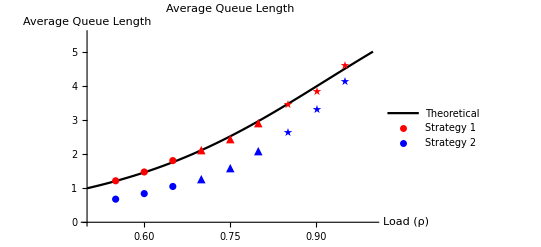

```mathematica
p1 =TheorPlot["Average Queue Length",L[ρ],{ρ,0.5,1},{0,5.5},"Load (ρ)","Average Queue Length"];
Show[
p1,
ListPlot[Transpose[{x1,S1y1}],PlotStyle->Red,PlotLegends->{"Strategy 1"}],
ListPlot[Transpose[{x2,S1y2}],PlotStyle->Red,PlotMarkers->"▲"],
ListPlot[Transpose[{x3,S1y3}],PlotStyle->Red,PlotMarkers->"★"],

ListPlot[Transpose[{x1,S2y1}],PlotStyle->Blue,PlotLegends->{"Strategy 2"}],
ListPlot[Transpose[{x2,S2y2}],PlotStyle->Blue,PlotMarkers->"▲"],
ListPlot[Transpose[{x3,S2y3}],PlotStyle->Blue,PlotMarkers->"★"]
]
```

## Avg Sojourn Time

### λ Plot (Set μ = 0.5) (λ → {0,1} )

```mathematica
x = {0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0};
S1y = ConstantArray[0,11];
S2y = ConstantArray[0,11];
```

#### Strategy 1 Data

```mathematica
S1y[[1]]=Mean[{∞}]; (*λ=0*)
S1y[[2]]=Mean[{2.81358176,2.83475860,2.83207586,2.83291027,2.73862840,2.84147374,2.84258868,2.80004901,2.77923150,2.83119199}];(*λ=0.1*)
S1y[[3]]=Mean[{1.79935562,1.83643982,1.89169390,1.84523658,1.84604295,1.78515374,1.82535414,1.90006331,1.85848296,1.82715428}];(*λ=0.2*)
S1y[[4]]=Mean[{1.74189267,1.77278498,1.70198137,1.69297520,1.70137984,1.65396446,1.71999639,1.81834663,1.62005137,1.69623777}];(*λ=0.3*)
S1y[[5]]=Mean[{1.93578952,1.80708930,1.71258729,1.78679873,1.79012153,1.83269854,1.89686116,1.84274355,1.83322636,1.93842355}];(*λ=0.4*)
S1y[[6]]=Mean[{2.07704372,2.08629478,2.14490980,2.19565977,1.95867324,2.15082653,2.10361202,2.15939524,2.11644579,2.11367681}]; (*λ=0.5*)
S1y[[7]]=Mean[{2.32797589,2.38871560,2.64483769,2.36895260,2.67264764,2.67252411,2.52264919,2.72369338,2.35110069,2.44533339}]; (*λ=0.6*)
S1y[[8]]=Mean[{2.78278393,2.91138933,3.14645367,3.00721159,3.11340963,3.25289972,3.10810542,2.91400409,2.74783930,3.19990098}]; (*λ=0.7*)
S1y[[9]]=Mean[{3.79253325,3.82941603,3.52095384,3.96262679,3.92803821,3.82492114,3.82957452,3.84029596,3.63396139,4.07360015}]; (*λ=0.8*)
S1y[[10]]=Mean[{4.68272912,4.71468203,4.29457237,4.49904664,4.71143118,4.35057620,4.82839938,4.85587240,4.70603549,4.40019867}]; (*λ=0.9*)
S1y[[11]]=Mean[{5.00694663,5.21161105,5.82765637,5.37998847,5.48824024,5.45233759,5.66345786,5.49111459,5.34533339,5.53350439}];(*λ=1.0*)
```

#### Strategy 2 Data

```mathematica
S2y[[1]]=Mean[{0}]; (*λ=0*)
S2y[[2]]=Mean[{0.64298712,0.66511966,0.63706049,0.66358655,0.65663172,0.63219891,0.66010143,0.62993353,0.65916873,0.63028134}]; (*λ=0.10*)
S2y[[3]]=Mean[{0.74110803,0.75653560,0.74897136,0.74813099,0.74582958,0.74937229,0.71061940,0.70798121,0.74878945,0.73921982}]; (*λ=0.20*)
S2y[[4]]=Mean[{0.89159127,0.87880935,0.86109516,0.84863259,0.88861808,0.87172985,0.85624369,0.86463984,0.84520114,0.85494139}]; (*λ=0.30*)
S2y[[5]]=Mean[{0.97773071,1.01114902,1.01733262,0.98475822,1.01066523,0.97663395,0.97904511,1.01865185,1.00358934,0.98406630}]; (*λ=0.40*)
S2y[[6]]=Mean[{1.15089730,1.15788111,1.12962018,1.19385412,1.14373902,1.17427127,1.16253843,1.17799091,1.16771198,1.17035346}]; (*λ=0.50*)
S2y[[7]]=Mean[{1.41669525,1.47449251,1.44969477,1.44764056,1.42844591,1.35350923,1.43679564,1.37294494,1.51207350,1.36332707}]; (*λ=0.60*)
S2y[[8]]=Mean[{1.85705489,1.65689851,1.98653231,1.99252938,1.80599003,1.95587753,1.79803494,1.84244317,1.86941940,1.80148358}]; (*λ=0.70*)
S2y[[9]]=Mean[{2.61016095,2.31216430,2.55554559,2.52040291,2.93317037,2.49208781,2.67387302,2.48838658,2.75076040,2.70121742}]; (*λ=0.80*)
S2y[[10]]=Mean[{3.79885694,3.68426667,3.90926969,3.66805024,3.82384740,3.95833224,3.83186956,3.57397071,3.88318643,3.67843784}]; (*λ=0.90*)
S2y[[11]]=Mean[{5.12833250,5.00836830,5.41503186,5.12415001,5.94154171,4.73831505,5.48599420,5.44738225,5.68194303,4.46558261}]; (*λ=1.00*)
```

#### Plot

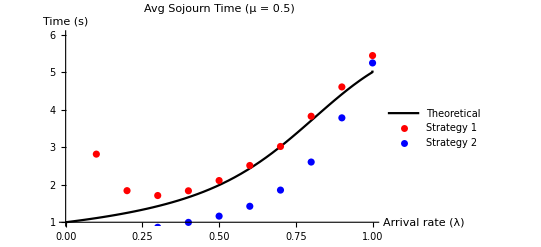

```mathematica
p1 =TheorPlot["Avg Sojourn Time (μ  = 0.5)",S2[λ/(2(0.5)),0.5],{λ,0,1},{1,6},"Arrival rate (λ)","Time (s)"];
Show[p1, S1Plot[x,S1y],S2Plot[x,S2y]]
```

### μ Plot (Set λ = 2) (μ → {1,10} )

```mathematica
x = {1,1.1,1.25,1.4,1.6,2,2.5,3.3,5,8,10};
S1y = ConstantArray[0,11];
S2y = ConstantArray[0,11];
```

#### Strategy 1 Data

```mathematica
S1y[[1]]=Mean[{2.47945363,2.87639322,2.61533687,2.74296000,2.59663451,2.86423400,2.81270753,2.63481124,2.77353385,2.93856173}]; (*μ=1*)
S1y[[2]]=Mean[{1.91427051,2.32821742,2.08951979,2.23466367,2.14155298,2.06456559,2.08516993,2.20123088,2.37264683,2.08008178}];(*μ=1.1*)
S1y[[3]]=Mean[{1.50902266,1.47657369,1.53018057,1.63632230,1.62214962,1.55433074,1.62551482,1.39018691,1.49267871,1.61671383}];(*μ=1.25*)
S1y[[4]]=Mean[{1.17196285,0.98168309,1.04566172,1.06843049,1.05897364,1.15079895,1.04361281,1.13152165,1.04665280,1.07709132}];(*μ=1.4*)
S1y[[5]]=Mean[{0.78380105,0.77689689,0.82865395,0.82181310,0.80788252,0.78340151,0.76923576,0.79497755,0.80933085,0.76781921}];(*μ=1.6*)
S1y[[6]]=Mean[{0.53716975,0.48688136,0.51007501,0.51453857,0.50781391,0.53097685,0.49874113,0.55953013,0.50831632,0.54575677}]; (*μ=2*)
S1y[[7]]=Mean[{0.35821047,0.37328502,0.35951389,0.37253318,0.37311616,0.36688632,0.37343511,0.34445226,0.37611168,0.35803461}]; (*μ=2.5*)
S1y[[8]]=Mean[{0.25720168,0.25801602,0.25718670,0.24688769,0.25866247,0.26941833,0.25414277,0.24737005,0.25908743,0.24684418}]; (*μ=3.3*)
S1y[[9]]=Mean[{0.19624340,0.18036522,0.18160159,0.18666127,0.18023727,0.18327461,0.18557650,0.18271133,0.18586738,0.18434164}]; (*μ=5*)
S1y[[10]]=Mean[{0.14806625,0.14846098,0.14697138,0.14629023,0.14950863,0.15012869,0.15063334,0.15190433,0.14577782,0.15332870}]; (*μ=8*)
S1y[[11]]=Mean[{0.13945912,0.14071287,0.14120501,0.14035143,0.14204008,0.13958869,0.13854743,0.14003991,0.13671653,0.14134506}];(*μ=10*)
```

#### Strategy 2 Data

```mathematica
S2y[[1]]=Mean[{2.83564540,2.40317412,2.49938627,3.00120026,2.60851609,2.82606899,3.01164201,2.88621444,2.64640112,2.61359832}]; (*μ=1.00*)
S2y[[2]]=Mean[{1.72999425,1.96711552,1.59658700,1.74357414,1.57675481,1.89924285,1.73137246,1.69897174,1.82990926,1.75330363}]; (*μ=1.10*)
S2y[[3]]=Mean[{1.13284832,1.00727651,1.01481410,1.09000477,1.05636577,1.06839864,1.07219708,0.99114529,1.00800771,1.11360881}]; (*μ=1.25*)
S2y[[4]]=Mean[{0.71321703,0.72095637,0.69166972,0.72604020,0.73789078,0.67212118,0.67041234,0.68623999,0.69065238,0.67634655}]; (*μ=1.40*)
S2y[[5]]=Mean[{0.44034116,0.50656120,0.48537844,0.47951589,0.47363406,0.47603401,0.50028738,0.50192548,0.49042808,0.47826508}]; (*μ=1.60*)
S2y[[6]]=Mean[{0.30039607,0.28637871,0.28279710,0.29615836,0.27542716,0.29994623,0.29651116,0.28985686,0.28370610,0.29917816}]; (*μ=2.00*)
S2y[[7]]=Mean[{0.19417977,0.19241421,0.20127005,0.19737440,0.20034698,0.19438559,0.19878715,0.19868916,0.19335701,0.19328857}]; (*μ=2.50*)
S2y[[8]]=Mean[{0.13339028,0.12868008,0.13379356,0.13157336,0.12695597,0.13147186,0.13014161,0.13129904,0.13462163,0.13335571}]; (*μ=3.30*)
S2y[[9]]=Mean[{0.07769799,0.07226369,0.07272492,0.07324172,0.07801694,0.07200038,0.07580947,0.07739401,0.07477830,0.07372428}]; (*μ=5.00*)
S2y[[10]]=Mean[{0.04275161,0.04183602,0.03970371,0.04122508,0.04252454,0.04293722,0.04405202,0.04220263,0.04094591,0.04210908}]; (*μ=8.00*)
S2y[[11]]=Mean[{0.03107348,0.03150622,0.02944916,0.03432063,0.03202210,0.03196085,0.03207649,0.02986135,0.03344013,0.03209804}]; (*μ=10.00*)
```

#### Plot

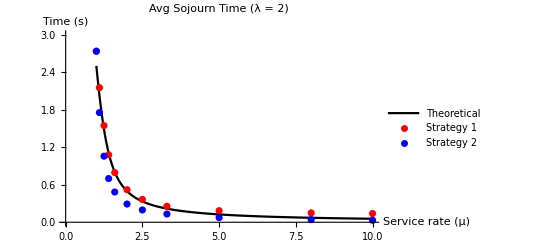

```mathematica
p1 =TheorPlot["Avg Sojourn Time (λ = 2)",S[2/(2μ),2],{μ,1,10},{0,3},"Service rate (μ)","Time (s)"];
Show[p1, S1Plot[x,S1y],S2Plot[x,S2y]]
```

### ρ Plot (Choose and λ, μ such that ρ -> {0, 1})

```mathematica
x1= {0.55,0.6,0.65}; (*ρ values*)
x2= {0.7,0.75,0.8}; (*ρ values*)
x3= {0.85,0.9,0.95}; (*ρ values*)

S1y1 = ConstantArray[0,3];
S1y2 = ConstantArray[0,3];
S1y3 = ConstantArray[0,3];

S2y1 = ConstantArray[0,3];
S2y2 = ConstantArray[0,3];
S2y3 = ConstantArray[0,3];
```

#### Strategy 1 Data

```mathematica
(*λ = 0.25*)
S1y1[[1]]=Mean[{4.72135415,4.72230803,4.67352388,4.90000283,4.88778317,4.89561737,4.83077360,4.79215317,5.05911920,5.07233792}]; (*μ=0.23*)
S1y1[[2]]=Mean[{6.28886239,5.57921692,5.98105561,5.66499248,5.76494792,5.54039308,5.69294477,5.95812140,6.08928448,5.92782592}]; (*μ=0.21*)
S1y1[[3]]=Mean[{7.92609097,7.68151180,7.55713062,7.35397752,7.13755399,7.67271764,7.56294738,7.26604568,7.71757806,7.08441050}]; (*μ=0.19*)
(*λ = 5*)
S1y2[[1]]=Mean[{0.43084284,0.48118611,0.45422295,0.39851286,0.41057291,0.41846249,0.45911733,0.41988843,0.40889369,0.43193356}]; (*μ=3.57*)
S1y2[[2]]=Mean[{0.53116625,0.51176062,0.52836064,0.46633860,0.53467665,0.50541376,0.55151669,0.48588614,0.50110429,0.50820201}]; (*μ=3.33*)
S1y2[[3]]=Mean[{0.64818897,0.59324477,0.60537847,0.65072739,0.62639326,0.67956945,0.59170580,0.57515330,0.61416363,0.61594998}]; (*μ=3.12*)
(*λ = 10*)
S1y3[[1]]=Mean[{0.34803252,0.38377314,0.35629511,0.33898764,0.37869737,0.38314559,0.32847514,0.35250012,0.36648361,0.35695547}]; (*μ=5.88*)
S1y3[[2]]=Mean[{0.43109182,0.41687027,0.40859153,0.44919113,0.43643186,0.44983987,0.41267184,0.43673640,0.39899137,0.44636610}]; (*μ=5.56*)
S1y3[[3]]=Mean[{0.50440591,0.46685148,0.48791622,0.44064471,0.44852981,0.48769741,0.47872383,0.49923382,0.51286672,0.49304150}]; (*μ=5.26*)
```

#### Strategy 2 Data

```mathematica
(*λ = 0.25*)
S2y1[[1]]=Mean[{2.75425464,2.76425762,2.64399249,2.63236164,2.63985455,2.76031039,2.86098919,2.73692376,2.84166187,2.72310545}]; (*μ=0.23*)
S2y1[[2]]=Mean[{3.35329531,3.31124239,3.28283613,3.29009127,3.34598210,3.42210113,3.41620882,3.39110561,3.49250460,3.44324307}]; (*μ=0.21*)
S2y1[[3]]=Mean[{4.45395982,4.12489245,4.56264976,4.21026700,4.27172019,4.70116098,4.49402635,4.34220217,4.34826737,4.02481361}]; (*μ=0.19*)
(*λ = 5*)
S2y2[[1]]=Mean[{0.26308928,0.23557873,0.26669950,0.26254708,0.26124198,0.25934379,0.23865563,0.25250456,0.25986946,0.25679595}]; (*μ=3.57*)
S2y2[[2]]=Mean[{0.32222126,0.33001679,0.34802807,0.32535703,0.32043255,0.33484454,0.31736309,0.34812487,0.32267855,0.32009036}]; (*μ=3.33*)
S2y2[[3]]=Mean[{0.41104307,0.46030821,0.40695432,0.37722552,0.40610124,0.41159707,0.39272597,0.38422833,0.40705925,0.41185291}]; (*μ=3.12*)
(*λ = 10*)
S2y3[[1]]=Mean[{0.25649693,0.28718888,0.27453427,0.26727239,0.27924677,0.26106532,0.27149758,0.27910018,0.26140068,0.26666242}]; (*μ=5.88*)
S2y3[[2]]=Mean[{0.36291813,0.34694550,0.33519566,0.35761294,0.34481674,0.32171440,0.33038516,0.36425768,0.31662573,0.31003779}]; (*μ=5.56*)
S2y3[[3]]=Mean[{0.41567388,0.42410042,0.40677401,0.42103129,0.43222979,0.44136934,0.42637343,0.42113894,0.39631975,0.42808081}]; (*μ=5.26*)
```

#### Plot

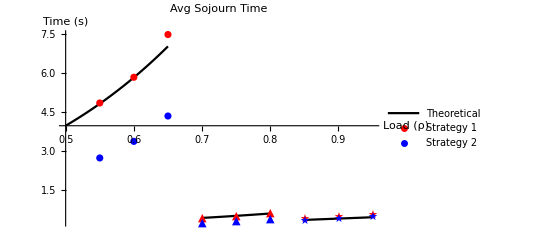

```mathematica
p1 =TheorPlot["Average Queue Length",L[ρ],{ρ,0.5,1},{0,5.5},"Load (ρ)","Average Queue Length"];
Show[
Plot[S[ρ,0.25],{ρ,0.5,0.65},PlotStyle->Black,PlotLegends->{"Theoretical"}],
Plot[S[ρ,5],{ρ,0.7,0.8},PlotStyle->Black],
Plot[S[ρ,10],{ρ,0.85,0.95},PlotStyle->Black],
ListPlot[Transpose[{x1,S1y1}],PlotStyle->Red,PlotLegends->{"Strategy 1"}],
ListPlot[Transpose[{x2,S1y2}],PlotStyle->Red,PlotMarkers->"▲"],
ListPlot[Transpose[{x3,S1y3}],PlotStyle->Red,PlotMarkers->"★"],

ListPlot[Transpose[{x1,S2y1}],PlotStyle->Blue,PlotLegends->{"Strategy 2"}],
ListPlot[Transpose[{x2,S2y2}],PlotStyle->Blue,PlotMarkers->"▲"],
ListPlot[Transpose[{x3,S2y3}],PlotStyle->Blue,PlotMarkers->"★"],
PlotRange->All,
AxesLabel->{"Load (ρ)","Time (s)"},
PlotLabel->"Avg Sojourn Time"
]
```

## End